## Twisted Bilayer, Isotropic Forces, Layer Coupling

```mathematica
ClearAll[ex, ey, n, latticepts,unitcellpts,dcutoff,bonds,segmentn,segments,qloop, freqs,D3x3]
```

```mathematica
(*Parameters*)
ebx={1,0,0};
eby={0,1,0};
lx=3;
ly=4;
lm=√(lx^2+ly^2);
θ=N[ArcTan[ly/lx]];
rot=({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}});
etx=rot.ebx;
ety=rot.eby;
(*Moire*)
eMx=(√(lx^2+ly^2))*etx;
eMy=(√(lx^2+ly^2))*ety;
(*Inverse*)
Gbx=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eby)/(ebx.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eby);
Gby=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).ebx)/(eby.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).ebx);
Gtx=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).ety)/(etx.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).ety);
Gty=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).etx)/(ety.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).etx);
GMx=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eMy)/(eMx.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eMy);
GMy=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eMx)/(eMy.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eMx);
(*Lattice Height*)
h=1;
(*Bond Distance Cutoff*)
dcutoff =1;
(*Create Momentum Loop*)
segmentn=50;
segments={{0,0,0},(1/2 GMx+1/2 GMy)};
qloop={};
For[s=1,s<Length[segments],s++,
For[i=0,i<=segmentn,i++,
AppendTo[qloop,segments[[s]]+i*((segments[[s+1]]-segments[[s]])/segmentn)]
]
]
ListPointPlot3D[qloop]
(*Dummy vars*)
n=50;
δ=.01;
(*Generate Unit cell points*)
unitcellpts={};
For[i=(-n )/2,i<=n/2,i++,
For[j=(-n)/2,j<=n/2,j++,
If[-δ<=((i*ebx+j*eby)/Norm[eMx]^2).eMx<=1-δ&&-δ<=((i*ebx+j*eby)/Norm[eMy]^2).eMy<=1-δ,
AppendTo[unitcellpts, i*ebx+j*eby];
];
]
]
For[i=(-n )/2,i<=n/2,i++,
For[j=(-n)/2,j<=n/2,j++,
If[-δ<=((i*etx+j*ety)/Norm[eMx]^2).eMx<=1-δ&&-δ<=((i*etx+j*ety)/Norm[eMy]^2).eMy<=1-δ,
AppendTo[unitcellpts, i*etx+j*ety+{0,0,h}];
];
]
]
(*Calculate Unit Cells*)
unitcells={};
xmin =Min[unitcellpts.eMx/(√(eMx.eMx))]-dcutoff;
xmax =Max[unitcellpts.eMx/(√(eMx.eMx))]+dcutoff;
ymin=Min[unitcellpts.eMy/(√(eMy.eMy))]-dcutoff;
ymax=Max[unitcellpts.eMy/(√(eMy.eMy))]+dcutoff;
nxmin=Floor[xmin/(√(eMx.eMx))];
nxmax = Ceiling[xmax/(√(eMx.eMx))];
nymin=Floor[ymin/(√(eMy.eMy))];
nymax=Ceiling[ymax/(√(eMy.eMy))];
For[i=nxmin,i<=nxmax,i++,
For[j=nymin,j<=nymax,j++,
AppendTo[unitcells, i*eMx + j*eMy]
];
];
```

-Graphics3D-

## One Vertical Bond

-Graphics3D-

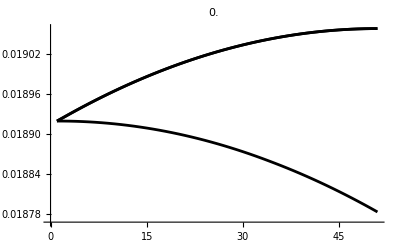
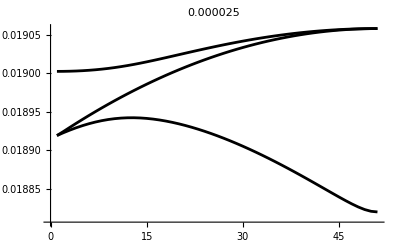
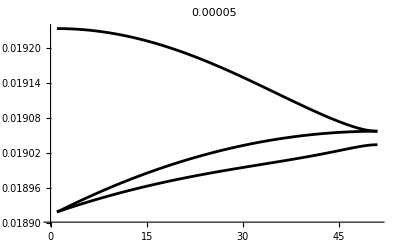
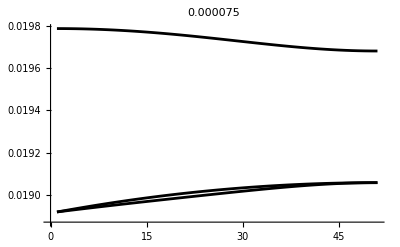
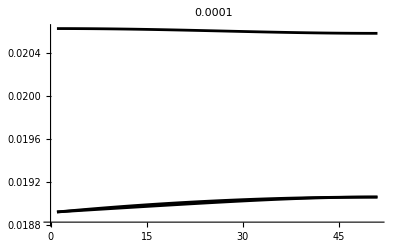

```mathematica
(*Generate Bonds*)
bonds={};
bondgraphics={};
Monitor[For[i=1,i<=Length[unitcellpts],i++,
For[j=1,j<=Length[unitcellpts],j++,
For[R=1,R<=Length[unitcells],R++,
d=Norm[unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]];
If[d!=0&&d<=dcutoff&&Abs[unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]][[3]]<=h/2,
dhat=1/d*(unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]);
AppendTo[bonds,{i, j,R,dhat,d}];
AppendTo[bondgraphics,Line[{unitcellpts[[i]],unitcellpts[[j]]+unitcells[[R]]}]];
];
]
]
],{i,j}]
(*Manually add in vertical bonds*)
(*(5,40), (8,33),(13,26),(18,49),(21,42)*)
c=Position[unitcells,{0.,0.,0.}][[1,1]];
AppendTo[bonds,{5,40,c,{0,0,h},h}];
AppendTo[bonds,{40,5,c,{0,0,-h},h}];
AppendTo[bondgraphics,Line[{unitcellpts[[5]],unitcellpts[[40]]}]];
Show[Graphics3D[bondgraphics],ListPointPlot3D[unitcellpts],Boxed->False]
(*Main Loop*)
freqs={};
Ain=1;
λin=10;
Amin=0;
Amax=.0001;
An=4;
dA=(Amax-Amin)/An;
Aouts=Table[Amin+dA*i,{i,0,An}];
λout=.1;
Monitor[For[a=1,a<=Length[Aouts],a++,
Aout=Aouts[[a]];
AppendTo[freqs,{}];
For[k=1,k<=Length[qloop],k++,
(*Momentum*)
q=qloop[[k]]; 
(*Dynamics Matrixes*)
DynamicsMatrix=ConstantArray[0,{Length[unitcellpts],Length[unitcellpts]}];
(*Loop over bonds*)
For[i=1,i<=Length[bonds],i++,
a1=bonds[[i]][[1]];
a2=bonds[[i]][[2]];
R=bonds[[i]][[3]];
dhat=bonds[[i]][[4]];
d=bonds[[i]][[5]];
If[Abs[d*dhat][[3]]<=h/2,
D3x3=Ain*ⅇ^(-λin*d),
D3x3=Aout/ⅇ^(-λout*h)*ⅇ^(-λout*d)];
DynamicsMatrix[[a1,a1]]+=1*D3x3;
DynamicsMatrix[[a1,a2]]+=-D3x3*ⅇ^(I*unitcells[[R]].q);
];
AppendTo[freqs[[-1]],√(Eigenvalues[DynamicsMatrix])]
]]
,{a,k}]
Table[ListLinePlot[Table[Re[freqs[[a]][[;;,i]]],{i,1,3}],PlotStyle->{{Black}},PlotRange->All,PlotLabel->Aouts[[a]]],{a,1,Length[Aouts]}]
```

## Two Vertical Bonds

$Aborted

-Graphics3D-

472

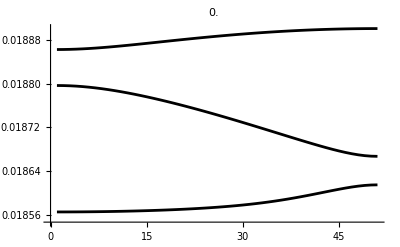
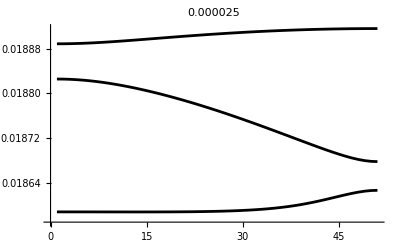
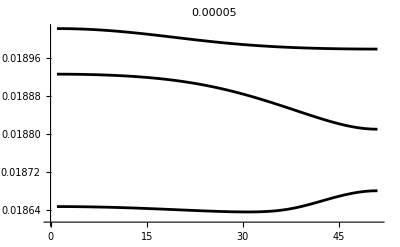
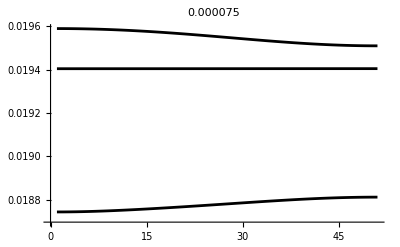
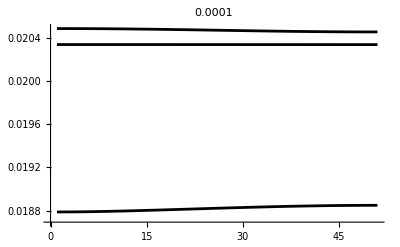

```mathematica
(*Generate Bonds*)
bonds={};
bondgraphics={};
Monitor[For[i=1,i<=Length[unitcellpts],i++,
For[j=1,j<=Length[unitcellpts],j++,
For[R=1,R<=Length[unitcells],R++,
d=Norm[unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]];
If[d!=0&&d<=dcutoff&&Abs[unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]][[3]]<=h/2,
dhat=1/d*(unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]);
AppendTo[bonds,{i, j,R,dhat,d}];
AppendTo[bondgraphics,Line[{unitcellpts[[i]],unitcellpts[[j]]+unitcells[[R]]}]];
];
]
]
],{i,j}]
(*Manually add in vertical bonds*)
(*(5,40), (8,33),(13,26),(18,49),(21,42)*)
c=Position[unitcells,{0.,0.,0.}][[1,1]];
AppendTo[bonds,{5,40,c,{0,0,h},h}];
AppendTo[bonds,{40,5,c,{0,0,-h},h}];
AppendTo[bondgraphics,Line[{unitcellpts[[5]],unitcellpts[[40]]}]];
AppendTo[bonds,{8,33,c,{0,0,h},h}];
AppendTo[bonds,{33,8,c,{0,0,-h},h}];
AppendTo[bondgraphics,Line[{unitcellpts[[8]],unitcellpts[[33]]}]];
Show[Graphics3D[bondgraphics],ListPointPlot3D[unitcellpts],Boxed->False]
Length[bonds]
(*Main Loop*)
freqs={};
Ain=1;
λin=10;
Amin=0;
Amax=.0001;
An=4;
dA=(Amax-Amin)/An;
Aouts=Table[Amin+dA*i,{i,0,An}];
λout=.1;
Monitor[For[a=1,a<=Length[Aouts],a++,
Aout=Aouts[[a]];
AppendTo[freqs,{}];
For[k=1,k<=Length[qloop],k++,
(*Momentum*)
q=qloop[[k]]; 
(*Dynamics Matrixes*)
DynamicsMatrix=ConstantArray[0,{Length[unitcellpts],Length[unitcellpts]}];
(*Loop over bonds*)
For[i=1,i<=Length[bonds],i++,
a1=bonds[[i]][[1]];
a2=bonds[[i]][[2]];
R=bonds[[i]][[3]];
dhat=bonds[[i]][[4]];
d=bonds[[i]][[5]];
If[Abs[d*dhat][[3]]<=h/2,
D3x3=Ain*ⅇ^(-λin*d),
D3x3=Aout/ⅇ^(-λout*h)*ⅇ^(-λout*d)];
DynamicsMatrix[[a1,a1]]+=1*D3x3;
DynamicsMatrix[[a1,a2]]+=-D3x3*ⅇ^(I*unitcells[[R]].q);
];
AppendTo[freqs[[-1]],ReverseSort[√(Eigenvalues[DynamicsMatrix])]]
]]
,{a,k}]
Table[ListLinePlot[Table[Re[freqs[[a]][[;;,i]]],{i,1,3}],PlotStyle->{{Black}},PlotRange->All,PlotLabel->Aouts[[a]]],{a,1,Length[Aouts]}]
```

## 3 Vertical Bonds

-Graphics3D-

206

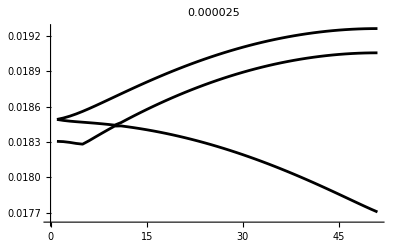
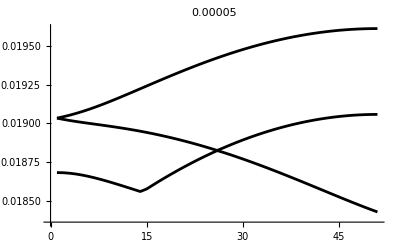
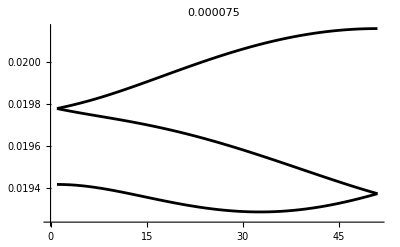
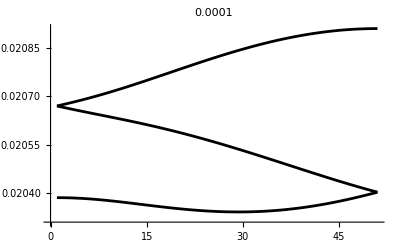

```mathematica
(*Generate Bonds*)
bonds={};
bondgraphics={};
Monitor[For[i=1,i<=Length[unitcellpts],i++,
For[j=1,j<=Length[unitcellpts],j++,
For[R=1,R<=Length[unitcells],R++,
d=Norm[unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]];
If[d!=0&&d<=dcutoff&&Abs[unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]][[3]]<=h/2,
dhat=1/d*(unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]);
AppendTo[bonds,{i, j,R,dhat,d}];
AppendTo[bondgraphics,Line[{unitcellpts[[i]],unitcellpts[[j]]+unitcells[[R]]}]];
];
]
]
],{i,j}]
(*Manually add in vertical bonds*)
(*(5,40), (8,33),(13,26),(18,49),(21,42)*)
c=Position[unitcells,{0.,0.,0.}][[1,1]];
AppendTo[bonds,{5,40,c,{0,0,h},h}];
AppendTo[bonds,{40,5,c,{0,0,-h},h}];
AppendTo[bondgraphics,Line[{unitcellpts[[5]],unitcellpts[[40]]}]];
AppendTo[bonds,{8,33,c,{0,0,h},h}];
AppendTo[bonds,{33,8,c,{0,0,-h},h}];
AppendTo[bondgraphics,Line[{unitcellpts[[8]],unitcellpts[[33]]}]];
AppendTo[bonds,{13,26,c,{0,0,h},h}];
AppendTo[bonds,{26,13,c,{0,0,-h},h}];
AppendTo[bondgraphics,Line[{unitcellpts[[13]],unitcellpts[[26]]}]];
Show[Graphics3D[bondgraphics],ListPointPlot3D[unitcellpts],Boxed->False]
Length[bonds]
(*Main Loop*)
freqs={};
Ain=1;
λin=10;
Amin=0;
Amax=.0001;
An=4;
dA=(Amax-Amin)/An;
Aouts=Table[Amin+dA*i,{i,1,An}];
λout=.1;
Monitor[For[a=1,a<=Length[Aouts],a++,
Aout=Aouts[[a]];
AppendTo[freqs,{}];
For[k=1,k<=Length[qloop],k++,
(*Momentum*)
q=qloop[[k]]; 
(*Dynamics Matrixes*)
DynamicsMatrix=ConstantArray[0,{Length[unitcellpts],Length[unitcellpts]}];
(*Loop over bonds*)
For[i=1,i<=Length[bonds],i++,
a1=bonds[[i]][[1]];
a2=bonds[[i]][[2]];
R=bonds[[i]][[3]];
dhat=bonds[[i]][[4]];
d=bonds[[i]][[5]];
If[Abs[d*dhat][[3]]<=h/2,
D3x3=Ain*ⅇ^(-λin*d),
D3x3=Aout/ⅇ^(-λout*h)*ⅇ^(-λout*d)];
DynamicsMatrix[[a1,a1]]+=1*D3x3;
DynamicsMatrix[[a1,a2]]+=-D3x3*ⅇ^(I*unitcells[[R]].q);
];
AppendTo[freqs[[-1]],√(Eigenvalues[DynamicsMatrix])]
]]
,{a,k}]
Table[ListLinePlot[Table[Re[freqs[[a]][[;;,i]]],{i,1,3}],PlotStyle->{{Black}},PlotRange->All,PlotLabel->Aouts[[a]]],{a,1,Length[Aouts]}]
```

## 4 Vertical Bonds

-Graphics3D-

208

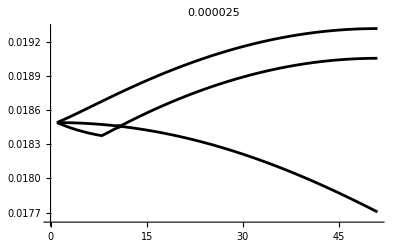
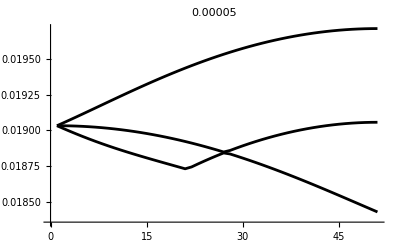
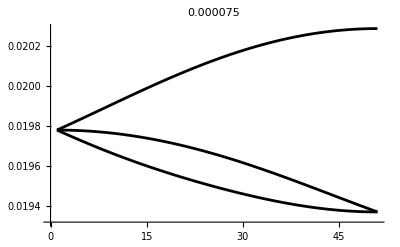
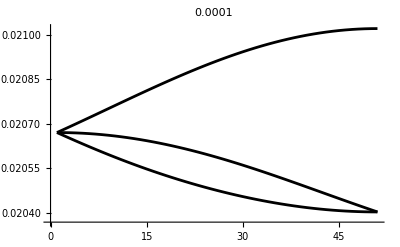

```mathematica
(*Generate Bonds*)
bonds={};
bondgraphics={};
Monitor[For[i=1,i<=Length[unitcellpts],i++,
For[j=1,j<=Length[unitcellpts],j++,
For[R=1,R<=Length[unitcells],R++,
d=Norm[unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]];
If[d!=0&&d<=dcutoff&&Abs[unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]][[3]]<=h/2,
dhat=1/d*(unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]);
AppendTo[bonds,{i, j,R,dhat,d}];
AppendTo[bondgraphics,Line[{unitcellpts[[i]],unitcellpts[[j]]+unitcells[[R]]}]];
];
]
]
],{i,j}]
(*Manually add in vertical bonds*)
(*(5,40), (8,33),(13,26),(18,49),(21,42)*)
c=Position[unitcells,{0.,0.,0.}][[1,1]];
AppendTo[bonds,{5,40,c,{0,0,h},h}];
AppendTo[bonds,{40,5,c,{0,0,-h},h}];
AppendTo[bondgraphics,Line[{unitcellpts[[5]],unitcellpts[[40]]}]];
AppendTo[bonds,{8,33,c,{0,0,h},h}];
AppendTo[bonds,{33,8,c,{0,0,-h},h}];
AppendTo[bondgraphics,Line[{unitcellpts[[8]],unitcellpts[[33]]}]];
AppendTo[bonds,{13,26,c,{0,0,h},h}];
AppendTo[bonds,{26,13,c,{0,0,-h},h}];
AppendTo[bondgraphics,Line[{unitcellpts[[13]],unitcellpts[[26]]}]];
AppendTo[bonds,{18,49,c,{0,0,h},h}];
AppendTo[bonds,{49,18,c,{0,0,-h},h}];
AppendTo[bondgraphics,Line[{unitcellpts[[18]],unitcellpts[[49]]}]];
Show[Graphics3D[bondgraphics],ListPointPlot3D[unitcellpts],Boxed->False]
Length[bonds]
(*Main Loop*)
freqs={};
Ain=1;
λin=10;
Amin=0;
Amax=.0001;
An=4;
dA=(Amax-Amin)/An;
Aouts=Table[Amin+dA*i,{i,1,An}];
λout=.1;
Monitor[For[a=1,a<=Length[Aouts],a++,
Aout=Aouts[[a]];
AppendTo[freqs,{}];
For[k=1,k<=Length[qloop],k++,
(*Momentum*)
q=qloop[[k]]; 
(*Dynamics Matrixes*)
DynamicsMatrix=ConstantArray[0,{Length[unitcellpts],Length[unitcellpts]}];
(*Loop over bonds*)
For[i=1,i<=Length[bonds],i++,
a1=bonds[[i]][[1]];
a2=bonds[[i]][[2]];
R=bonds[[i]][[3]];
dhat=bonds[[i]][[4]];
d=bonds[[i]][[5]];
If[Abs[d*dhat][[3]]<=h/2,
D3x3=Ain*ⅇ^(-λin*d),
D3x3=Aout/ⅇ^(-λout*h)*ⅇ^(-λout*d)];
DynamicsMatrix[[a1,a1]]+=1*D3x3;
DynamicsMatrix[[a1,a2]]+=-D3x3*ⅇ^(I*unitcells[[R]].q);
];
AppendTo[freqs[[-1]],√(Eigenvalues[DynamicsMatrix])]
]]
,{a,k}]
Table[ListLinePlot[Table[Re[freqs[[a]][[;;,i]]],{i,1,3}],PlotStyle->{{Black}},PlotRange->All,PlotLabel->Aouts[[a]]],{a,1,Length[Aouts]}]
```

## 5 Vertical Bonds

-Graphics3D-

210

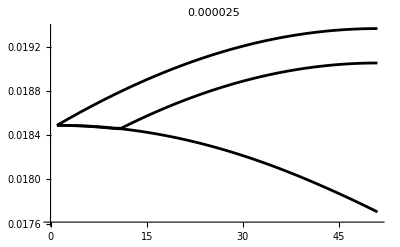
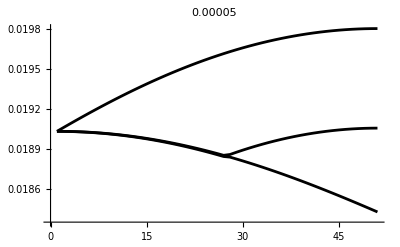
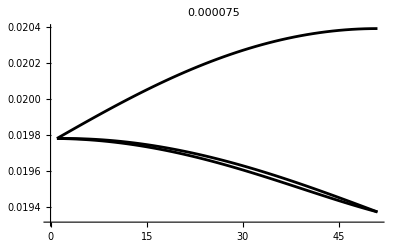
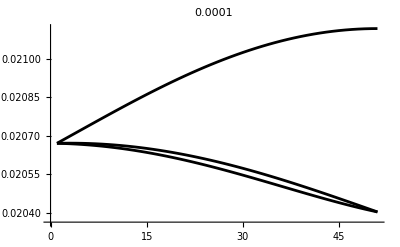

```mathematica
(*Generate Bonds*)
bonds={};
bondgraphics={};
Monitor[For[i=1,i<=Length[unitcellpts],i++,
For[j=1,j<=Length[unitcellpts],j++,
For[R=1,R<=Length[unitcells],R++,
d=Norm[unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]];
If[d!=0&&d<=dcutoff&&Abs[unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]][[3]]<=h/2,
dhat=1/d*(unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]);
AppendTo[bonds,{i, j,R,dhat,d}];
AppendTo[bondgraphics,Line[{unitcellpts[[i]],unitcellpts[[j]]+unitcells[[R]]}]];
];
]
]
],{i,j}]
(*Manually add in vertical bonds*)
(*(5,40), (8,33),(13,26),(18,49),(21,42)*)
c=Position[unitcells,{0.,0.,0.}][[1,1]];
AppendTo[bonds,{5,40,c,{0,0,h},h}];
AppendTo[bonds,{40,5,c,{0,0,-h},h}];
AppendTo[bondgraphics,Line[{unitcellpts[[5]],unitcellpts[[40]]}]];
AppendTo[bonds,{8,33,c,{0,0,h},h}];
AppendTo[bonds,{33,8,c,{0,0,-h},h}];
AppendTo[bondgraphics,Line[{unitcellpts[[8]],unitcellpts[[33]]}]];
AppendTo[bonds,{13,26,c,{0,0,h},h}];
AppendTo[bonds,{26,13,c,{0,0,-h},h}];
AppendTo[bondgraphics,Line[{unitcellpts[[13]],unitcellpts[[26]]}]];
AppendTo[bonds,{18,49,c,{0,0,h},h}];
AppendTo[bonds,{49,18,c,{0,0,-h},h}];
AppendTo[bondgraphics,Line[{unitcellpts[[18]],unitcellpts[[49]]}]];
AppendTo[bonds,{21,42,c,{0,0,h},h}];
AppendTo[bonds,{42,21,c,{0,0,-h},h}];
AppendTo[bondgraphics,Line[{unitcellpts[[21]],unitcellpts[[42]]}]];
Show[Graphics3D[bondgraphics],ListPointPlot3D[unitcellpts],Boxed->False]
Length[bonds]
(*Main Loop*)
freqs={};
Ain=1;
λin=10;
Amin=0;
Amax=.0001;
An=4;
dA=(Amax-Amin)/An;
Aouts=Table[Amin+dA*i,{i,1,An}];
λout=.1;
Monitor[For[a=1,a<=Length[Aouts],a++,
Aout=Aouts[[a]];
AppendTo[freqs,{}];
For[k=1,k<=Length[qloop],k++,
(*Momentum*)
q=qloop[[k]]; 
(*Dynamics Matrixes*)
DynamicsMatrix=ConstantArray[0,{Length[unitcellpts],Length[unitcellpts]}];
(*Loop over bonds*)
For[i=1,i<=Length[bonds],i++,
a1=bonds[[i]][[1]];
a2=bonds[[i]][[2]];
R=bonds[[i]][[3]];
dhat=bonds[[i]][[4]];
d=bonds[[i]][[5]];
If[Abs[d*dhat][[3]]<=h/2,
D3x3=Ain*ⅇ^(-λin*d),
D3x3=Aout/ⅇ^(-λout*h)*ⅇ^(-λout*d)];
DynamicsMatrix[[a1,a1]]+=1*D3x3;
DynamicsMatrix[[a1,a2]]+=-D3x3*ⅇ^(I*unitcells[[R]].q);
];
AppendTo[freqs[[-1]],ReverseSort[√(Eigenvalues[DynamicsMatrix])]]
]]
,{a,k}]
Table[ListLinePlot[Table[Re[freqs[[a]][[;;,i]]],{i,1,3}],PlotStyle->{{Black}},PlotRange->All,PlotLabel->Aouts[[a]]],{a,1,Length[Aouts]}]
```